```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

```mathematica
Subscript[r, o]=60/2 10^-3 ; (*meters*)
Subscript[r, i]=44/2  10^-3; (*meters*)
Subscript[r, f]=30/2  10^-3; (*meters*)
Subscript[J, 1]=(π ((Subscript[r, o])^4-(Subscript[r, i])^4))/2; (*meters^4*)
Subscript[J, 2]=(π (Subscript[r, o])^4)/2; (*meters^4*)
Subscript[J, 3]=(π (Subscript[r, f])^4)/2; (*meters^4*)
ClearAll[J]
J[X_]:=Piecewise[
{{Subscript[J, 1],0≤ X<0.6},
{Subscript[J, 2],0.6≤ X<0.8},
{Subscript[J, 3],0.8≤ X<1.2}}
] (*meters^4*)

T=250; (*In newton.meter *)
G=77 10^9 (*N/m^2 or Pa*);
L=1.2  (*in meters*);
```

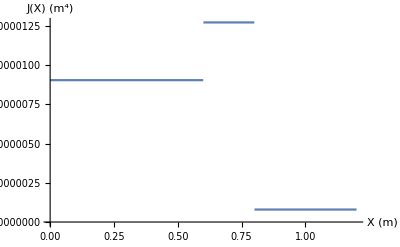

```mathematica
Plot[J[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```

```mathematica
Subscript[θ, L]=T/G Integrate[1/J[X],{X,0,L}]
```

0.0189958

```mathematica
Subscript[θ, L]/Degree
```

1.08838